# Finite Difference Methods

## Fully explicit method with expanding space grid

Forward-difference (fully explicit) method for a potential step to the limiting current region for the reaction O+e⇌R.

Version 1.30
copyright © 2002-Year Michael Honeychurch

## Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"],Clear["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
```

```mathematica
SetOptions[ListPlot3D,
AspectRatio-> 1,
AxesLabel->{
Style["k",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["j",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["c  ",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Plain,FontWeight-> Bold]},
ImageSize->288,
ViewPoint->{2,-.5,1},
Mesh->False];
```

```mathematica
SetOptions[ListPlot,
Frame->True,
FrameStyle->AbsoluteThickness[1],
GridLines->None,
ImageSize->400,
PlotStyle->{Blue,AbsoluteThickness[1]},
Joined->True];
```

```mathematica
optionA={
Axes-> False,
Frame-> True,
FrameLabel-> {
Style["k",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["z  ",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
None,
None},
FormatType-> TraditionalForm,
Frame-> False,
Joined-> False,
PlotRegion-> {{0,1},{0.1,0.9}},
PlotLabel-> None,
PlotStyle-> Thickness[0],
Prolog-> {Green,AbsolutePointSize[4.5]}
};
```

```mathematica
optionB={
Axes-> False,
Frame-> True,
FrameLabel-> {
Style["k",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["z  ",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
None,
None},
FormatType-> TraditionalForm,
Frame-> False,
Joined-> True,
PlotRegion-> {{0,1},{0.1,0.9}},
PlotLabel-> None,
PlotStyle-> {Red,Thickness[0.002]}};
```

```mathematica
$Line=0;
```

## Make Grid

```mathematica
Clear[makeGrid,n,m];
makeGrid[m_Integer,n_Integer]:=
	Module[{j,k,c},
		c=Table[1.,{m},{n}];
		For[j=1,j≤m,j++,c⟦j,1⟧=1.](*initial condition*);
		For[k=2,k≤n,k++,
				c⟦1,k⟧=0.(*boundary condition*);
				c⟦m,k⟧=1.;(*boundary condition*)
];
c]
```

```mathematica
makeGrid[5,5]//MatrixForm
```

(1. | 0. | 0. | 0. | 0.
1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1.)

## Set Up Solution

```mathematica
Clear[variableExplicitSolve1];

(*procedural method in which α=Δy/2*)

variableExplicitSolve1[m_Integer,n_Integer,d_][yLim_,α_]:=
	Module[{p,k,x,c},
x=Exp[-2*(p-1)/(m-1)*yLim];
c =makeGrid[m,n];
		For[k=2,k≤n,k++,
			For[p=2,p≤m-1,p++,
				c⟦p,k⟧=(d*x*(1-α)*c⟦p+1,k-1⟧)+((1-2*d*x)*c⟦p,k-1⟧)+(d*x*(1+α)*c⟦p-1,k-1⟧)];];c];
```

```mathematica
Clear[variableExplicitSolve2];

variableExplicitSolve2[m_Integer,n_Integer,d_][yLim_,α_]:=Module[{p,solveNext},
solveNext[start_]:=Flatten[{0.,
With[{kernel=Unevaluated[{d*Exp[-2*(p-1)/(m-1)*yLim]*(1+α),(1- 2*d*Exp[-2*(p-1)/(m-1)*yLim]),d*Exp[-2*(p++-1)/(m-1)*yLim]*(1-α)}]},
p=2;
ListCorrelate[kernel,start]
],1.}];

NestList[solveNext,ConstantArray[1.,{m}],n]]
```

## Set Parameter Values

```mathematica
Clear[n,a,yLim,m,α,𝔻];

n=400;

a=3.0;

yLim=Log[1.+6*a];

𝔻=0.4;(*model diffusion coefficient*)

m=1+Ceiling[yLim/a*√(𝔻*(n-1))];

α=yLim/(2*(m-1));
```

## Solve It

```mathematica
Clear[c];
Timing[
c=variableExplicitSolve1[m,n,𝔻][yLim,α];
c=Transpose[c];
c=Rest[c];]
```

{0.283051,Null}

```mathematica
Clear[c];

Timing[
c=variableExplicitSolve2[m,n,𝔻][yLim,α];
c=Rest[c];]
```

{0.257637,Null}

## Plot Current vs. Time

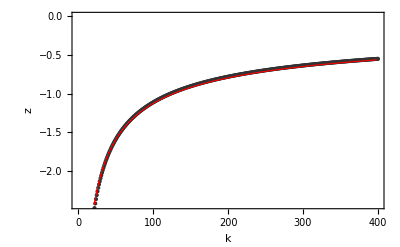

```mathematica
Clear[i,z];

i=Map[((-4*#⟦2⟧+#⟦3⟧)*0.5*√(𝔻*(n-1)))&,c];

z=Table[-1/Sqrt[Pi*(k-1)/(n-1)],{k,2,n-1}]//N;

Show[ListPlot[i,optionA],ListPlot[z,optionB]]
```